# Kotashevich_S_N Lab_work_7

## Элементарная описательная статистика

```mathematica
data={6.5,3.8,6.6,5.7,6.0,6.4,5.3};
```

```mathematica
Covariance[data,RandomReal[1,Length[data]]]
```

0.086669

```mathematica
CentralMoment[data,2]
```

0.825306

```mathematica
Quartiles[data]
```

{5.4,6.,6.475}

```mathematica
heights = Quantity[{133,143,131,140,145,136,131,136,143,136,133,145,147,
        150,150,146,137,143,132,142,145,136,144,135,141},"Centimeters"];
```

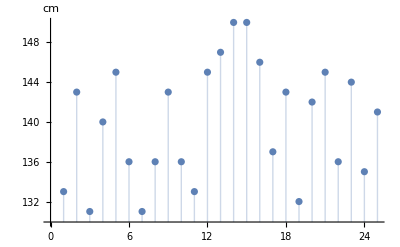

```mathematica
ListPlot[heights,Filling->Axis,AxesLabel->Automatic]
```

```mathematica
Median[heights]
```

141 cm

```mathematica
Mean[heights]
```

140 cm

```mathematica
Quantile[heights,{0.25,0.5,0.75}]
```

{136 cm,141 cm,145 cm}

```mathematica
Quartiles[heights] // N
```

{135.75 cm,141. cm,145. cm}

```mathematica
Sqrt[Variance[heights]] // N
```

5.88076 cm

## Миссинг дата

```mathematica
ElementData[117,"MeltingPoint"]
```

Missing[NotAvailable]

```mathematica
IsotopeData[{94,236},"DecayEnergies"]
```

{5867.07 keV,Missing[NotAvailable],Missing[NotAvailable],-1588.01 keV}

```mathematica
DeleteMissing[%]
```

{5867.07 keV,-1588.01 keV}

```mathematica
IsotopeData[{94,236},"DecayEnergies"]/.Missing[_]->Nothing
```

{5867.07 keV,-1588.01 keV}

```mathematica
Cases[IsotopeData[{94,236},"DecayEnergies"], _Quantity]
```

{5867.07 keV,-1588.01 keV}

```mathematica
DeleteCases[IsotopeData[{94,236},"DecayEnergies"], _Missing]
```

{5867.07 keV,-1588.01 keV}

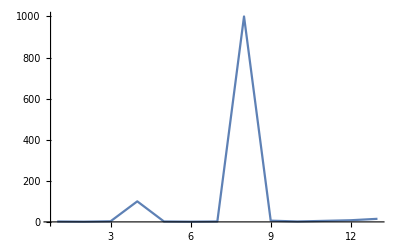

```mathematica
data3={2,1,3,100,2,1,2,1000,6,2,5,8,15};
ListLinePlot[data3,PlotRange->All]
```

```mathematica
data4 = DeleteAnomalies[data3]
```

{2,1,2,1,2,6,2,5,15}

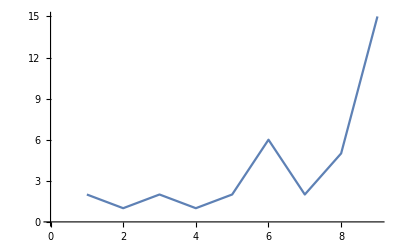

```mathematica
ListLinePlot[data4]
```

```mathematica
FindAnomalies[data3]
```

{3,100,1000,8}

```mathematica
data=Values@ExampleData[{"Dataset","Planets"}]["Jupiter","Moons"]
```

Dataset[<>]

```mathematica
SynthesizeMissingValues[data]
```

Dataset[<>]

## Подмножества

```mathematica
Gather[{a,b,a,d,b}]
```

{{a,a},{b,b},{d}}

```mathematica
Split[{a,a,a,b,b,a,a,c}]
```

{{a,a,a},{b,b},{a,a},{c}}

```mathematica
meddata={{drugB,67,18},{drugB,48,18},{drugA,33,16},{drugB,76,33},{drugB,33,3},{placebo,40,15},{drugB,78,28},{drugB,54,13},{placebo,46,23},{drugA,36,12},{drugA,69,30},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24},{placebo,25,9},{drugB,75,25},{drugB,22,3},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34},{drugB,52,16}};
```

```mathematica
Gather[meddata, First[#1]==First[#2]&]
```

{{{drugB,67,18},{drugB,48,18},{drugB,76,33},{drugB,33,3},{drugB,78,28},{drugB,54,13},{drugB,75,25},{drugB,22,3},{drugB,52,16}},{{drugA,33,16},{drugA,36,12},{drugA,69,30},{drugA,78,40},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,40,15},{placebo,46,23},{placebo,77,37},{placebo,25,9},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}}}

```mathematica
GatherBy[meddata, First]
```

{{{drugB,67,18},{drugB,48,18},{drugB,76,33},{drugB,33,3},{drugB,78,28},{drugB,54,13},{drugB,75,25},{drugB,22,3},{drugB,52,16}},{{drugA,33,16},{drugA,36,12},{drugA,69,30},{drugA,78,40},{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,40,15},{placebo,46,23},{placebo,77,37},{placebo,25,9},{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}}}

```mathematica
SplitBy[meddata, First]
```

{{{drugB,67,18},{drugB,48,18}},{{drugA,33,16}},{{drugB,76,33},{drugB,33,3}},{{placebo,40,15}},{{drugB,78,28},{drugB,54,13}},{{placebo,46,23}},{{drugA,36,12},{drugA,69,30},{drugA,78,40}},{{placebo,77,37}},{{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,25,9}},{{drugB,75,25},{drugB,22,3}},{{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}},{{drugB,52,16}}}

```mathematica
Split[meddata, First[#1]==First[#2]&]
```

{{{drugB,67,18},{drugB,48,18}},{{drugA,33,16}},{{drugB,76,33},{drugB,33,3}},{{placebo,40,15}},{{drugB,78,28},{drugB,54,13}},{{placebo,46,23}},{{drugA,36,12},{drugA,69,30},{drugA,78,40}},{{placebo,77,37}},{{drugA,79,36},{drugA,45,16},{drugA,36,18},{drugA,58,24}},{{placebo,25,9}},{{drugB,75,25},{drugB,22,3}},{{placebo,51,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}},{{drugB,52,16}}}

```mathematica
TakeList[meddata, {2}]
```

{{{drugB,67,18},{drugB,48,18}}}

```mathematica
TakeList[meddata, {2, 3}]
```

{{{drugB,67,18},{drugB,48,18}},{{drugA,33,16},{drugB,76,33},{drugB,33,3}}}

```mathematica
SortBy[meddata,#⟦2⟧&]
```

{{drugB,22,3},{placebo,25,9},{placebo,27,8},{drugA,33,16},{drugB,33,3},{drugA,36,12},{drugA,36,18},{placebo,40,15},{drugA,45,16},{placebo,46,23},{placebo,47,20},{drugB,48,18},{placebo,51,25},{drugB,52,16},{drugB,54,13},{drugA,58,24},{drugB,67,18},{drugA,69,30},{placebo,69,34},{drugB,75,25},{drugB,76,33},{placebo,77,37},{drugA,78,40},{drugB,78,28},{drugA,79,36}}

```mathematica
DeleteDuplicatesBy[meddata, #[[3]]&]
```

{{drugB,67,18},{drugA,33,16},{drugB,76,33},{drugB,33,3},{placebo,40,15},{drugB,78,28},{drugB,54,13},{placebo,46,23},{drugA,36,12},{drugA,69,30},{drugA,78,40},{placebo,77,37},{drugA,79,36},{drugA,58,24},{placebo,25,9},{drugB,75,25},{placebo,27,8},{placebo,47,20},{placebo,69,34}}

```mathematica
Union[meddata]
```

{{drugA,33,16},{drugA,36,12},{drugA,36,18},{drugA,45,16},{drugA,58,24},{drugA,69,30},{drugA,78,40},{drugA,79,36},{drugB,22,3},{drugB,33,3},{drugB,48,18},{drugB,52,16},{drugB,54,13},{drugB,67,18},{drugB,75,25},{drugB,76,33},{drugB,78,28},{placebo,25,9},{placebo,27,8},{placebo,40,15},{placebo,46,23},{placebo,47,20},{placebo,51,25},{placebo,69,34},{placebo,77,37}}